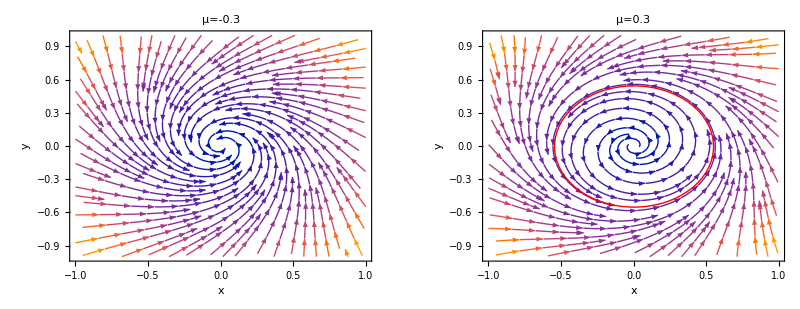

```mathematica
GraphicsRow[{With[{μ=-0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},AspectRatio->0.8,PlotLabel->"μ=-0.3",FrameLabel->{"x","y"}]],With[{μ=0.3},StreamPlot[{μ x-y-x(x^2+y^2),x+μ y-y(x^2+y^2)},{x,-1,1},{y,-1,1},Epilog->{Red,Circle[{0,0},√0.3]},AspectRatio->0.8,PlotLabel->"μ=0.3",FrameLabel->{"x","y"}]]}]
```